```mathematica
RamanujanSum[q_,n_]:=∑_(a=1)^Min[q,n] If[Divisible[q,a]==True&&Divisible[n,a]==True,1,0]MoebiusMu[q/a]a
CohenMuSum[q_,n_,b_]:=∑_(a=1)^Min[q,n] If[Divisible[q,a]==True&&Divisible[n,a^b]==True,1,0]MoebiusMu[q/a] a^b
DivisorBeta[k_,n_,b_]:=∑_(d=1)^n If[Divisible[n,d^b]==True,1,0] d^(b*k)
CohenMoment[y_,x_,b_]:=∑_(n=1)^y ∑_(q=1)^x CohenMuSum[q,n,b]
CohenMoment2[y_,x_,b_]:=∑_(n=1)^y (∑_(q=1)^x CohenMuSum[q,n,b])^2
f[β_,s_]=(Zeta[1-s/β]Zeta[2+s-β])/(Zeta[1+s])^2 1/((1+s)^2(β-s));
```

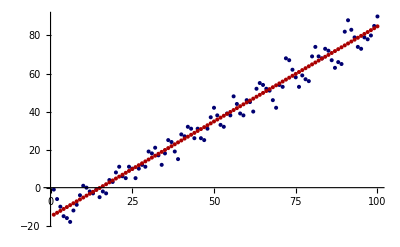

```mathematica
β=1;x=10;DiscretePlot[{CohenMoment[y,x,β],y-x^(1+β)/(2(1+β)Zeta[1+β])},{y,1,x^(1+β)},AxesOrigin->{0,0},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red]}]
```

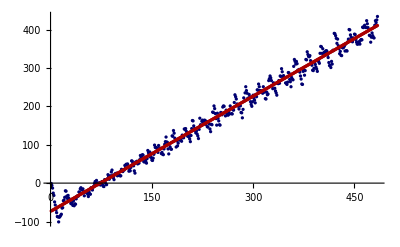

```mathematica
β=1;x=22;DiscretePlot[{CohenMoment[y,x,β],y-x^(1+β)/(2(1+β)Zeta[1+β])},{y,1,x^(1+β)},AxesOrigin->{0,0},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red]}]
```

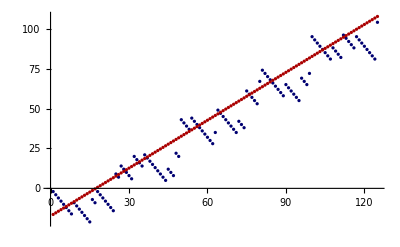

```mathematica
β=2;x=5;DiscretePlot[{CohenMoment[y,x,β],y-x^(1+β)/(2(1+β)Zeta[1+β])},{y,1,x^(1+β)},AxesOrigin->{0,0},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red]}]
```

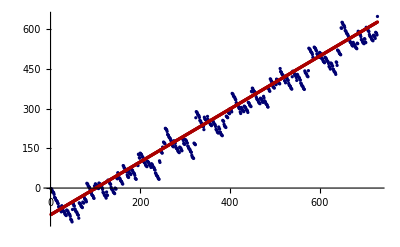

```mathematica
β=2;x=9;DiscretePlot[{CohenMoment[y,x,β],y-x^(1+β)/(2(1+β)Zeta[1+β])},{y,1,x^(1+β)},AxesOrigin->{0,0},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red]}]
```

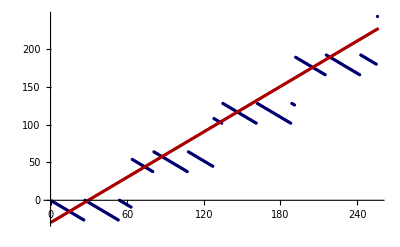

```mathematica
β=3;x=4;DiscretePlot[{CohenMoment[y,x,β],y-x^(1+β)/(2(1+β)Zeta[1+β])},{y,1,x^(1+β)},AxesOrigin->{0,0},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red]}]
```

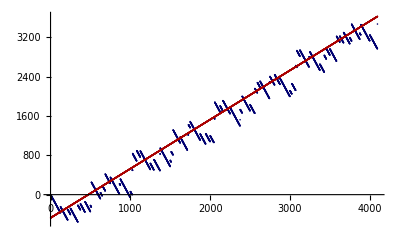

```mathematica
β=3;x=8;DiscretePlot[{CohenMoment[y,x,β],y-x^(1+β)/(2(1+β)Zeta[1+β])},{y,1,x^(1+β)},AxesOrigin->{0,0},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red]}]
```

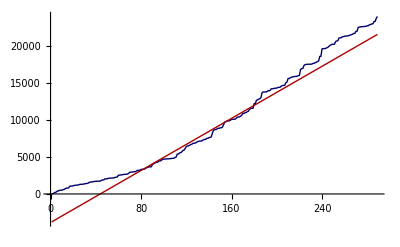

```mathematica
β=1;x=17;d=2;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])-x^(2+2β)/(2(1+β)^2(Zeta[1+β])^2)},{y,1,x^(2β)},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red],Darker[Green]}]
```

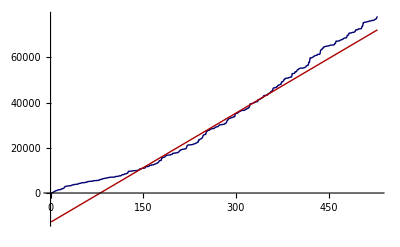

```mathematica
β=1;x=23;d=2;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])-x^(2+2β)/(2(1+β)^2(Zeta[1+β])^2)},{y,1,x^(2β)},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red],Darker[Green]}]
```

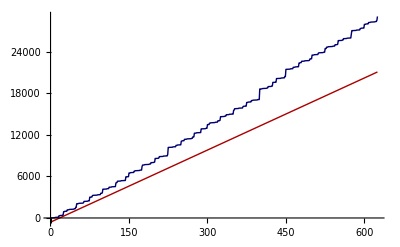

```mathematica
β=2;x=5;d=2;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])-x^(2+2β)/(2(1+β)^2(Zeta[1+β])^2)},{y,1,x^(2β)},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red],Darker[Green]}]
```

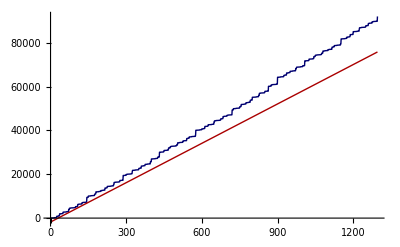

```mathematica
β=2;x=6;d=2;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])-x^(2+2β)/(2(1+β)^2(Zeta[1+β])^2)},{y,1,x^(2β)},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red],Darker[Green]}]
```

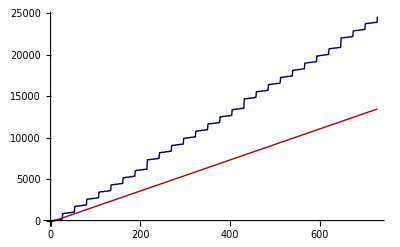

```mathematica
β=3;x=3;d=2;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])-x^(2+2β)/(2(1+β)^2(Zeta[1+β])^2)},{y,1,x^(2β)},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red],Darker[Green]}]
```

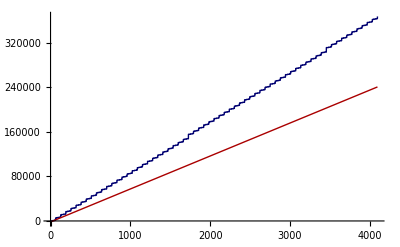

```mathematica
β=3;x=4;d=2;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])-x^(2+2β)/(2(1+β)^2(Zeta[1+β])^2)},{y,1,x^(2β)},Filling->None,PlotStyle->{Darker[Darker[Blue]],Darker[Red],Darker[Green]}]
```

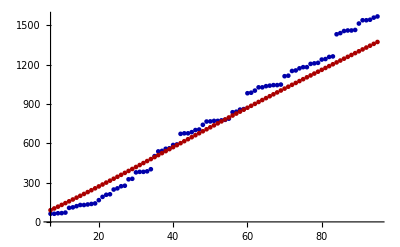

```mathematica
x=7;β=1;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

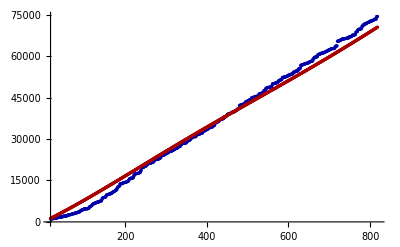

```mathematica
x=17;β=1;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

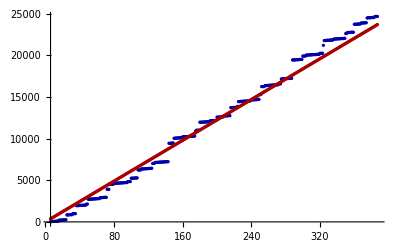

```mathematica
x=6;β=2;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

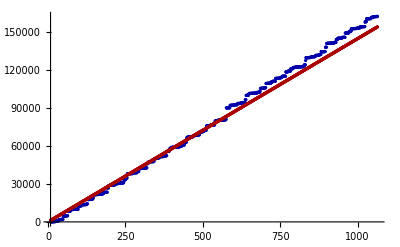

```mathematica
x=8;β=2;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

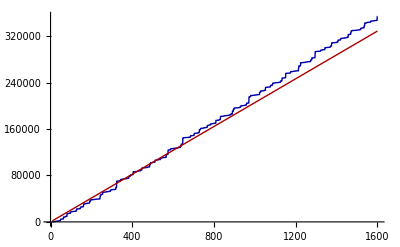

```mathematica
x=9;β=2;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

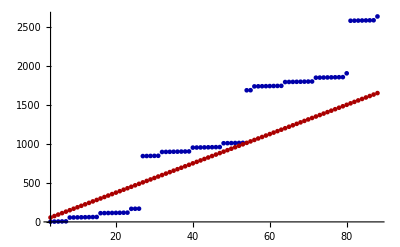

```mathematica
x=3;β=3;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

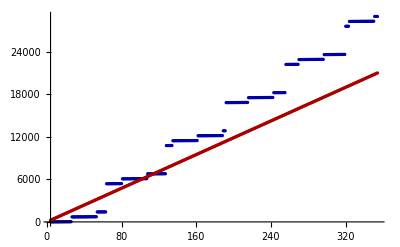

```mathematica
x=4;β=3;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

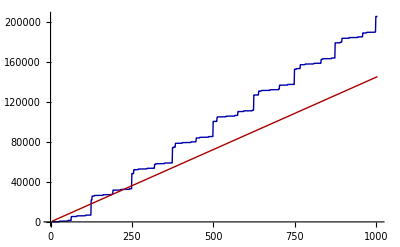

```mathematica
x=5;β=3;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```

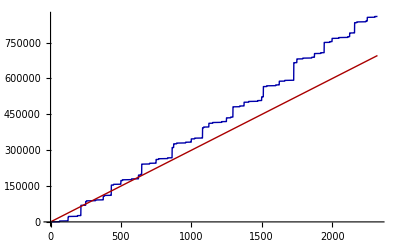

```mathematica
x=6;β=3;B=1;DiscretePlot[{CohenMoment2[y,x,β],(y*x^(1+β))/((1+β)Zeta[1+β])+(y*x^2)/Zeta[2] Re[NIntegrate[1/(2π)f[β,ⅈ*t] ⅇ^(-ⅈ*t*y^(1/β)*x^-2),{t,-2,2}]]},{y,x,x^(1+β)(Log[x])^B},Filling->None,PlotStyle->{Darker[Blue],Darker[Red]}]
```